```mathematica
(*parameters single cell model*)
b1=0.31;b2=0.18;gamma=0.27;alpha=0.94;vs=0.80;tita=0.11; beta=0.88;
(*parameters coupled system*)
k=0.3;a3=0.26;de=0.85;b4=0.35;a5=0.10;b5=0.65;
(*goodwin*)
n=15;
(*light*)
L1=0.0;L2=0.0;Tld=24;
(*tiempo*)
tmin=0;tmax=3000;
(*osciladores*)
nodes=10;
(*FUNCIONES*)
L[t_]:=L1+L2*UnitStep[Sin[Pi*t/12]]
Lv2[t_]:=L2 (1+Sin[2 Pi t/Tld])
M[t_]:=Sum[Y[i,t],{i,1,nodes}]/nodes
```

```mathematica
(* CONDICIONES INICIALES *)
ciX=(X[#1,0]==0.17&)/@Range[nodes];
ciY=Table[Y[j,0]==j/4,{j,1,nodes}];
ciZ=(Z[#1,0]==0.5&)/@Range[nodes];
ciS=(S[#1,0]==0.32&)/@Range[nodes];
ciU=(U[#1,0]==0.4&)/@Range[nodes];
ciV=(V[#1,0]==0.1&)/@Range[nodes];

(******* ECUACIONES DIFERENCIALES *********)
(* MIEMBROS DE LA DERECHA DE LAS EC. DIF. *)
fX=Table[vs/(1+(Z[j,t]^n))-b1 X[j,t],{j,1,nodes}];
fY=Table[alpha X[j,t]-(b2/(1+tita V[j,t] )+Lv2[t])*Y[j,t],{j,1,nodes}];
fZ=Table[beta Y[j,t]-gamma Z[j,t],{j,1,nodes}];
fS=Table[a3 Y[j,t]-de S[j,t],{j,1,nodes}];
fU=Table[k Sum[S[i,t],{i,1,nodes}]-b4 U[j,t],{j,1,nodes}];
fV=Table[a5 U[j,t]-b5 V[j,t],{j,1,nodes}];


(* VECTORES DE LAS POBLACIONES Y SUS DERIVADAS *)
vecX=(X[#1,t]&)/@Range[nodes];
vecdX=(D[X[#1,t], t]&)/@Range[nodes];
vecY=(Y[#1,t]&)/@Range[nodes];
vecdY=(D[Y[#1,t], t]&)/@Range[nodes];
vecZ=(Z[#1,t]&)/@Range[nodes];
vecdZ=(D[Z[#1,t], t]&)/@Range[nodes];
vecS=(S[#1,t]&)/@Range[nodes];
vecdS=(D[S[#1,t], t]&)/@Range[nodes];
vecU=(U[#1,t]&)/@Range[nodes];
vecdU=(D[U[#1,t], t]&)/@Range[nodes];
vecV=(V[#1,t]&)/@Range[nodes];
vecdV=(D[V[#1,t], t]&)/@Range[nodes];

(* ARMO LAS ECUACIONES DIFERENCIALES *)
(* Transpose es un truquito que genera una lista de pares. @@ (apply) le cambia el head, de List a Equal. Map le aplica esta función a cada uno de los pares de la lista. *)
eqsX=(Equal@@#1&)/@Transpose[{vecdX,fX}];
eqsY=(Equal@@#1&)/@Transpose[{vecdY,fY}];
eqsZ=(Equal@@#1&)/@Transpose[{vecdZ,fZ}];
eqsS=(Equal@@#1&)/@Transpose[{vecdS,fS}];
eqsU=(Equal@@#1&)/@Transpose[{vecdU,fU}];
eqsV=(Equal@@#1&)/@Transpose[{vecdV,fV}];

(* SOLUCION DE LA ECUACION DIFERENCIAL *)
sol=NDSolve[
Join[eqsX,eqsY,eqsZ,eqsS,eqsU,eqsV,ciX,ciY,ciZ,ciS,ciU,ciV],Join[vecX,vecY,vecZ,vecS,vecU,vecV],{t,tmin,tmax},MaxSteps->10^6,PrecisionGoal->5,AccuracyGoal->5];
```

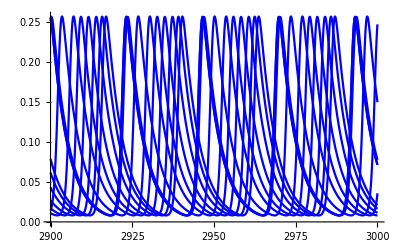

```mathematica
Plot[Evaluate[Map[#/.sol&,vecX]],{t,2900,3000},PlotStyle->{Blue}]
```

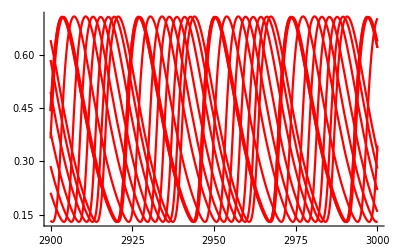

```mathematica
Plot[Evaluate[Map[#/.sol&,vecY]],{t,2900,3000},PlotStyle->{Red}]
```

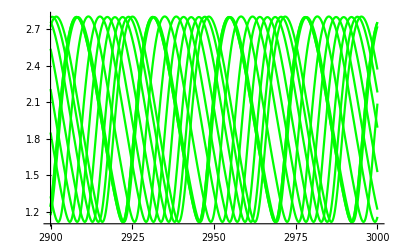

```mathematica
Plot[Evaluate[Map[#/.sol&,vecZ]],{t,2900,3000},PlotStyle->{Green}]
```

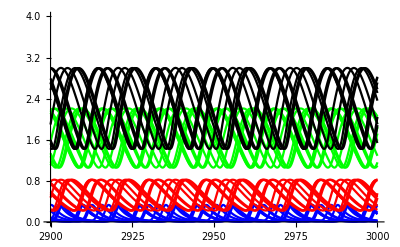

```mathematica
Show[Plot[Evaluate[Map[#/.sol&,vecX]],{t,2900,3000},PlotStyle->{Blue},PlotRange->{{2900,3000},{0,4}}],Plot[Evaluate[Map[#/.sol&,vecY]],{t,2900,3000},PlotStyle->{Red},PlotRange->{{2900,3000},{0,4}}],Plot[Evaluate[Map[#/.sol&,vecZ]],{t,2900,3000},PlotStyle->{Green},PlotRange->{{2900,3000},{0,4}}],Plot[Evaluate[Map[#/.sol&,vecX+vecY+vecZ]],{t,2900,3000},PlotStyle->{Black},PlotRange->{{2900,3000},{0,4}}]]
```

```mathematica
tmin1=1000;tmax1=1500;
```

```mathematica
ag=(Sum[Evaluate[{M[t]}/.sol],{t,tmin1,tmax1}]/(tmax1-tmin1))^2;
ag2=Sum[Evaluate[{M[t]^2}/.sol],{t,tmin1,tmax1}]/(tmax1-tmin1);
Ag1=ag2-ag
by[i_]:=Sum[Evaluate[{Y[i,t]^2}/.sol],{t,tmin1,tmax1}]/(tmax1-tmin1)
by2[i_]:=(Sum[Evaluate[{Y[i,t]}/.sol],{t,tmin1,tmax1}]/(tmax1-tmin1))^2
Bg1=(Sum[by[i],{i,1,nodes}]-Sum[by2[i],{i,1,nodes}])/nodes
Rg=Ag1/Bg1
```

{{0.0298264}}

{{0.0298264}}

{{1.}}